## Universidade Federal do Paraná Departamento de Informática Cássio Jandir Pagnoncelli, kimble9t (em) gmail (ponto) com

# Splines and Bézier curves

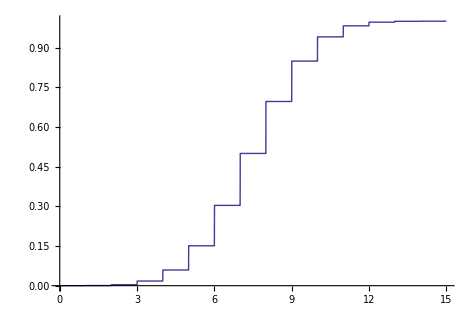

```mathematica
(* Set cdf to be the CDF of binomial distribution and plot its possible values. *)
cdf[x_]:=Sum[PDF[BinomialDistribution[15,0.5],j],{j,0,x}]
Plot[cdf[j],{j,0,15}]
```

-Graphics-

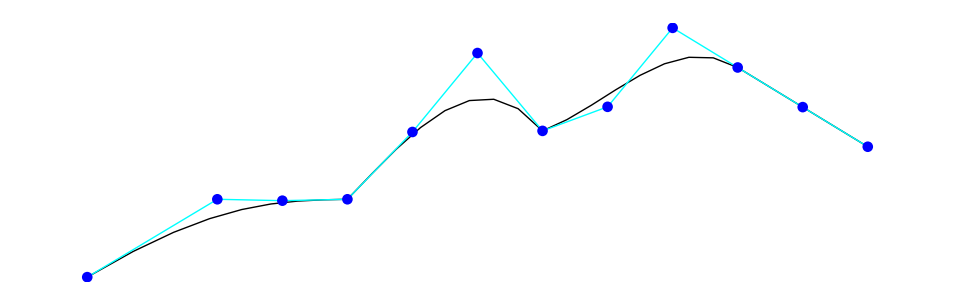

```mathematica
(* Random process starts at point (0,0). The other values are filled by uniform-randomly chosen elements of `cdf'. *)
length = 10;
v={{0,0}};
For[i=0,i≤length,i=i+1;
v=Append[v,{i+1,v[[i]][[2]]+(-1)^RandomInteger[1] cdf[RandomInteger[15]]}]
];
(* Plots the fitted spline and bézier curves to given stochastic process `v'. *)
Graphics[{BSplineCurve[v],Cyan,Line[v],Blue,PointSize[0.008],Point[v]}]
Graphics[{BezierCurve[v],Cyan,Line[v],Blue,PointSize[0.008],Point[v]}]
```

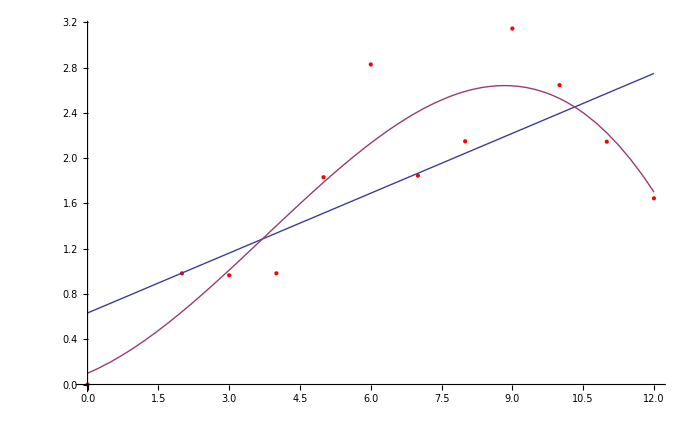

```mathematica
(* It is much better than linear regression fitting *)
line=Fit[v,{1,x},x];
parabola=Fit[v,{1,x,x^2,x^3},x];
Show[ListPlot[v,PlotStyle->Red],Plot[{line,parabola},{x,0,2+length}]]
```